```mathematica
file1 = "G:\\Studia\\IV\\MO\\Laboratoria\\9\\Program9\\Program9\\results_three0.dat";
file2 = "G:\\Studia\\IV\\MO\\Laboratoria\\9\\Program9\\Program9\\results_three1.dat";
file3 = "G:\\Studia\\IV\\MO\\Laboratoria\\9\\Program9\\Program9\\results_three2.dat";
file4= "G:\\Studia\\IV\\MO\\Laboratoria\\9\\Program9\\Program9\\results_numerow0.dat";
file5 = "G:\\Studia\\IV\\MO\\Laboratoria\\9\\Program9\\Program9\\results_numerow1.dat";
file6 = "G:\\Studia\\IV\\MO\\Laboratoria\\9\\Program9\\Program9\\results_numerow2.dat";
errorthreepoints = "G:\\Studia\\IV\\MO\\Laboratoria\\9\\Program9\\Program9\\errors_three.dat";
errornumerow = "G:\\Studia\\IV\\MO\\Laboratoria\\9\\Program9\\Program9\\errors_numerow.dat";
```

```mathematica
res1 = ReadList[file1, {Real, Real}];
res2 = ReadList[file2, {Real, Real}];
res3 = ReadList[file3, {Real, Real}];
res4 = ReadList[file4, {Real, Real}];
res5= ReadList[file5, {Real, Real}];
res6 = ReadList[file6, {Real, Real}];
errorsthreepoints= ReadList[errorthreepoints, {Real, Real}];
errorsnumerow= ReadList[errornumerow, {Real, Real}];
```

```mathematica
"Dyskretyzacja trzypunktowa:"
dp1 = (Abs[Part[Part[errorsthreepoints,1], 2]-Part[Part[errorsthreepoints,25], 2]]) / (Abs[Part[Part[errorsthreepoints, 1], 1] - Part[Part[errorsthreepoints,25], 1]])
```

Dyskretyzacja trzypunktowa:

2.00323

```mathematica
"Dyskretyzacja Numerow'a:"
dp2 = (Abs[Part[Part[errorsnumerow,1], 2]-Part[Part[errorsnumerow,5], 2]]) / (Abs[Part[Part[errorsnumerow, 1], 1] - Part[Part[errorsnumerow,5], 1]])
```

Dyskretyzacja Numerow'a:

3.99487

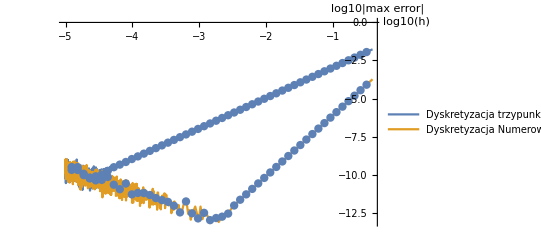

```mathematica
ListLinePlot[{errorsthreepoints, errorsnumerow},AxesLabel->{"log10(h)", "log10|max error|"}, PlotLegends->{"Dyskretyzacja trzypunktowa", "Dyskretyzacja Numerow'a"}, AxesLabel->Automatic,Mesh->50, PlotRange->All]
```

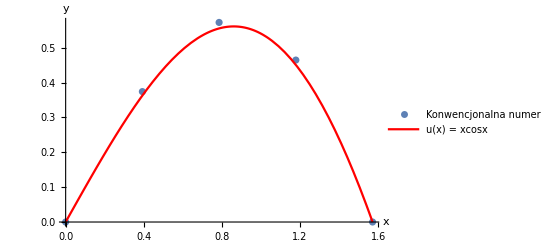

```mathematica
Show[ListPlot[res1,AxesLabel->{"x", "y"}, PlotLegends->{"Konwencjonalna numerycznie (h = 0.3927)"}], Plot[x*Cos[x], {x, 0, π/2}, PlotLegends->{"u(x) = xcosx"}, PlotStyle->{Red}]]
```

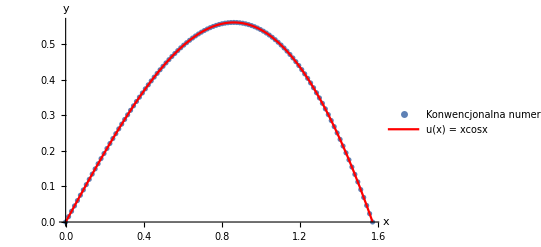

```mathematica
Show[ListPlot[res2,AxesLabel->{"x", "y"}, PlotLegends->{"Konwencjonalna numerycznie (h = 0.0151)"}], Plot[x*Cos[x], {x, 0, π/2}, PlotLegends->{"u(x) = xcosx"}, PlotStyle->{Red}]]
```

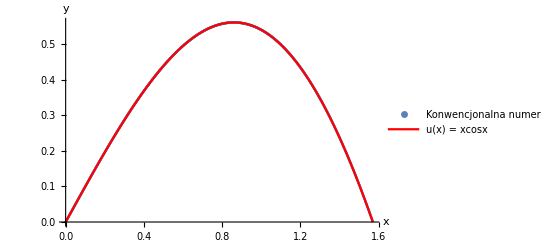

```mathematica
Show[ListPlot[res3,AxesLabel->{"x", "y"}, PlotLegends->{"Konwencjonalna numerycznie (h = 0.0015)"}], Plot[x*Cos[x], {x, 0, π/2}, PlotLegends->{"u(x) = xcosx"}, PlotStyle->{Red}]]
```

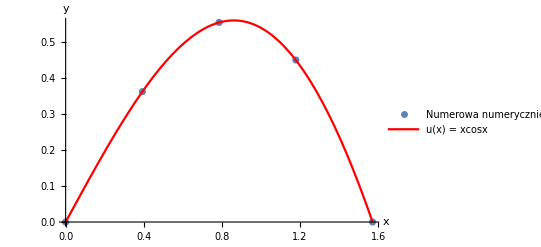

```mathematica
Show[ListPlot[res4,AxesLabel->{"x", "y"}, PlotLegends->{"Numerowa numerycznie (h = 0.3927)"}], Plot[x*Cos[x], {x, 0, π/2}, PlotLegends->{"u(x) = xcosx"}, PlotStyle->{Red}]]
```

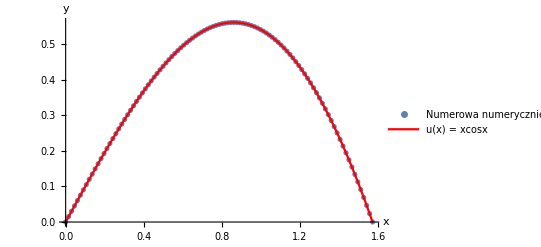

```mathematica
Show[ListPlot[res5,AxesLabel->{"x", "y"}, PlotLegends->{"Numerowa numerycznie (h = 0.0151)"}], Plot[x*Cos[x], {x, 0, π/2}, PlotLegends->{"u(x) = xcosx"}, PlotStyle->{Red}]]
```

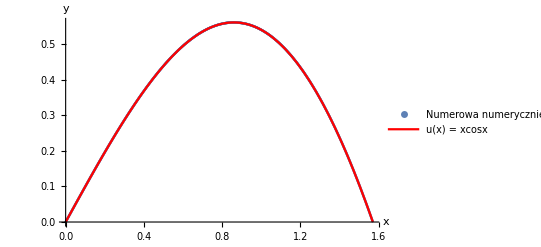

```mathematica
Show[ListPlot[res6,AxesLabel->{"x", "y"}, PlotLegends->{"Numerowa numerycznie (h = 0.0015)"}], Plot[x*Cos[x], {x, 0, π/2}, PlotLegends->{"u(x) = xcosx"}, PlotStyle->{Red}]]
```